```mathematica
轨道的傅立叶级数分解
```

{1.54293,{t→0.422836}}

{1.54293,{t→2.02034}}

basic freq = 0.625976 Hz

an | bn
0.593999 | 0
-0.343003 | 1.28388
0.0257235 | 0.147953
0.0144595 | 0.0209434
0.00439752 | 0.00260529
0.00112174 | 0.000116327
0.000250094 | -0.0000851561
0.0000467863 | -0.0000444585
6.02643×10^-6 | -0.0000151281
-2.13527×10^-7 | -4.22478×10^-6
-5.09694×10^-7 | -1.01548×10^-6
-2.32317×10^-7 | -2.17952×10^-7
-7.78194×10^-8 | -5.33733×10^-8
-2.17501×10^-8 | -2.85779×10^-8
-5.44385×10^-9 | -2.71751×10^-8
-1.50308×10^-9 | -2.69842×10^-8
-5.25835×10^-10 | -2.623×10^-8
-4.44539×10^-10 | -2.5142×10^-8
-4.76386×10^-10 | -2.36913×10^-8

an | bn
-0.726566 | 0
1.29188 | 0.326627
0.147986 | -0.0271079
0.0208734 | -0.014622
0.00258416 | -0.00441663
0.000111376 | -0.00112334
-0.000086145 | -0.000249983
-0.0000445976 | -0.0000466881
-0.0000151089 | -6.00336×10^-6
-4.18444×10^-6 | 2.08051×10^-7
-9.76202×10^-7 | 4.97087×10^-7
-1.82094×10^-7 | 2.1882×10^-7
-2.07451×10^-8 | 6.51005×10^-8
1.81676×10^-9 | 1.01937×10^-8
1.26766×10^-9 | -5.30379×10^-9
-5.00951×10^-10 | -8.54731×10^-9
-1.28987×10^-9 | -8.81702×10^-9
-1.53129×10^-9 | -8.31843×10^-9
-1.3446×10^-9 | -7.71483×10^-9

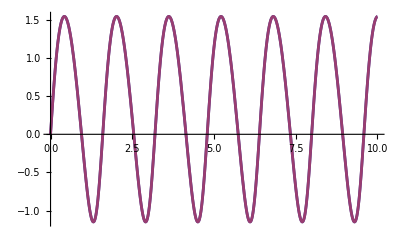

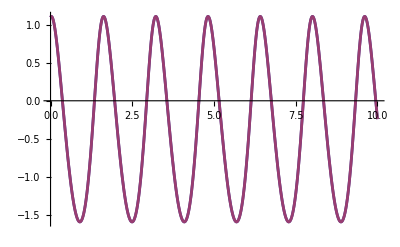

```mathematica
tm=10;coef=4.0 π^2;
xinitial={0,6.5};yinitial={1.1,0.8};
equ={x''[t]==-(coef*x[t])/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-(coef*y[t])/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equ,{x,y},{t,0,tm},MaxSteps->∞];
{x,y}={x,y}/.s[[1]];
(*finding period and basic frequence*)
peak1=FindMaximum[x[t],{t,0.5}]
peak2=FindMaximum[x[t],{t,2}]
T=(t/.peak2[[2]])-(t/.peak1[[2]]);
Print["basic freq = ",1/T," Hz"];
ω0=2π/T;
(*....finding harmonic coefficent.....*)
xcoef={{"an","bn"}};
a0x=2NIntegrate[x[t],{t,0,T}]/T;
AppendTo[xcoef,{a0x,0}];
Do[
a=2NIntegrate[x[t] Cos[j ω0 t],{t,0,T}]/T;
b=2NIntegrate[x[t] Sin[j ω0 t],{t,0,T}]/T;
AppendTo[xcoef,{a,b}],{j,18}]
ycoef={{"an","bn"}};
a0y=2NIntegrate[y[t],{t,0,T}]/T;
AppendTo[ycoef,{a0y,0}];
Do[
a=2NIntegrate[y[t] Cos[j ω0 t],{t,0,T}]/T;
b=2NIntegrate[y[t] Sin[j ω0 t],{t,0,T}]/T;
AppendTo[ycoef,{a,b}],{j,18}]
(*.........display coefficents.........*)
xcoef//TableForm
ycoef//TableForm
(*constructing functions*)
xf=a0x/2;yf=a0y/2;
Do[
xf=xf+xcoef[[j,1]] Cos[(j-2) ω0 t]+
xcoef[[j,2]] Sin[(j-2) ω0 t];
yf=yf+ycoef[[j,1]] Cos[(j-2) ω0 t]+
ycoef[[j,2]] Sin[(j-2) ω0 t],{j,3,20}]
(*.........comparing.........*)
Plot[{x[t],xf},{t,0,tm},
PlotStyle->Thickness[0.005],
AxesStyle->Thickness[0.003]]
Plot[{y[t],yf},{t,0,tm},
PlotStyle->Thickness[0.005],
AxesStyle->Thickness[0.003]]
Clear[x,y]
```